```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
fRandomFunction[x_,y_]:=PDF[MultinormalDistribution[{3,3},{{0.5,0},{0,0.5}}],{x,y}]+PDF[MultinormalDistribution[{6,6},{{0.6,-0.5},{-0.5,0.6}}],{x,y}]+PDF[MultinormalDistribution[{6,6},{{1,0.5},{0.5,1}}],{x,y}]+PDF[MultinormalDistribution[{6,4},{{0.6,0.5},{0.5,0.6}}],{x,y}]+PDF[MultinormalDistribution[{2,8},{{0.2,0},{0,0.2}}],{x,y}]
```

```mathematica
xTicks =Table[{i,100i},{i,2,10,2}];
```

```mathematica
Show[Plot3D[{fRandomFunction[x,y]},{x,0,10},{y,0,10},AxesLabel->{"East, km","North, km", ""},PlotRange->{Full,Full,{0,1}},ColorFunction->"BrassTones",Mesh->None,PlotPoints->20,Ticks->{xTicks,xTicks,None},ViewPoint->{1.4610778682878827,-1.9342706141474402,2.3608999669712687},ViewVertical->{0.,0.,1.}],Plot3D[1,{x,0,10},{y,0,10},AxesLabel->{"East, km","North, km", ""},PlotRange->Full,PlotStyle->{RGBColor[0.91,0.79,0.02],Opacity[0.2]},Mesh->None,PlotPoints->20,Ticks->{xTicks,xTicks,None}]]
```

-Graphics3D-

```mathematica
ColorFunction[
```

```mathematica
fSelectNewSite[aCurrentLocation_,aSigma_]:=Mod[aCurrentLocation+RandomVariate[MultinormalDistribution[{0,0},{{aSigma,0},{0,aSigma}}],1][[1]],10]
```

```mathematica
fStep[aCurrentLocation_,aSigma_]:=Module[{aNewLocation=fSelectNewSite[aCurrentLocation,aSigma],aCurrentB=fRandomFunction@@aCurrentLocation,aNewB,r,p=RandomReal[]},aNewB=fRandomFunction@@aNewLocation; r=aNewB/aCurrentB; If[r>p,aNewLocation,aCurrentLocation]]
```

```mathematica
lShortList=NestList[fStep[#,1]&,{1,1},1000];
lMediumList=NestList[fStep[#,1]&,{1,1},10000];
lLongList=NestList[fStep[#,1]&,{1,1},100000];
```

```mathematica
fConvertToLine[lList__,aValue_]:=Line[Join@@@Flatten[Thread[{lList,List/@ConstantArray[aValue,Length@lList]}],0]]
```

```mathematica
g3=Histogram3D[lLongList,{0.25},ChartStyle->{Opacity[1]},AxesLabel->{"East, km","North, km", ""},PlotRange->Full,ColorFunction->"BrassTones",Ticks->{xTicks,xTicks,None},ViewPoint->{1.4610778682878827,-1.9342706141474402,2.3608999669712687},ViewVertical->{0.,0.,1.},PlotLabel->"n = 100,000"]
```

-Graphics3D-

```mathematica
g2=Histogram3D[lMediumList,{0.25},ChartStyle->{Opacity[1]},AxesLabel->{"East, km","North, km", ""},PlotRange->Full,ColorFunction->"BrassTones",Ticks->{xTicks,xTicks,None},ViewPoint->{1.4610778682878827,-1.9342706141474402,2.3608999669712687},ViewVertical->{0.,0.,1.},PlotLabel->"n = 10,000"]
```

-Graphics3D-

```mathematica
g1=Histogram3D[lShortList,{0.25},ChartStyle->{Opacity[1]},AxesLabel->{"East, km","North, km", ""},PlotRange->Full,ColorFunction->"BrassTones",Ticks->{xTicks,xTicks,None},ViewPoint->{1.4610778682878827,-1.9342706141474402,2.3608999669712687},ViewVertical->{0.,0.,1.},PlotLabel->"n = 1,000"]
```

-Graphics3D-

```mathematica
aDist=MixtureDistribution[{1,1,1,1,1},{MultinormalDistribution[{3,3},{{0.5,0},{0,0.5}}],MultinormalDistribution[{6,6},{{0.6,-0.5},{-0.5,0.6}}],MultinormalDistribution[{6,6},{{1,0.5},{0.5,1}}],MultinormalDistribution[{6,4},{{0.6,0.5},{0.5,0.6}}],MultinormalDistribution[{2,8},{{0.2,0},{0,0.2}}]}];
```

```mathematica
gActual=Histogram3D[RandomVariate[aDist,1000000],{0.25},ChartStyle->{Opacity[1]},AxesLabel->{"East, km","North, km", ""},PlotRange->Full,ColorFunction->"BrassTones",Ticks->{xTicks,xTicks,None},ViewPoint->{1.4610778682878827,-1.9342706141474402,2.3608999669712687},ViewVertical->{0.,0.,1.},PlotLabel->"actual"]
```

-Graphics3D-

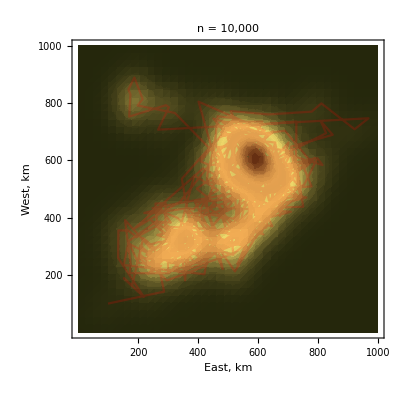

```mathematica
gb1=Show[SmoothDensityHistogram[lShortList,Mesh->20,PlotRange->{{0,10},{0,10}},Frame->{True,True,False,False},PlotLabel->"n = 10,000",FrameLabel->{"East, km","North, km"},FrameTicks->{xTicks,xTicks},ColorFunction->"BrassTones"],ListLinePlot[lShortList,PlotRange->{{0,10},{0,10}},PlotStyle->{Red,Opacity[0.2]}]]
```

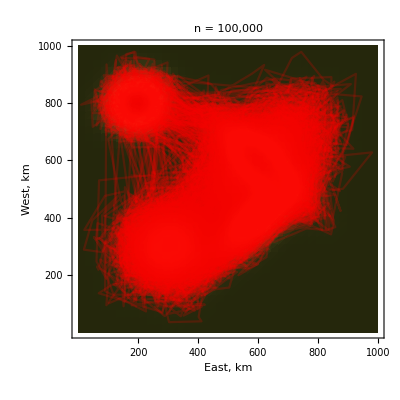

```mathematica
gb3=Show[SmoothDensityHistogram[lLongList,Mesh->20,PlotRange->{{0,10},{0,10}},Frame->{True,True,False,False},PlotLabel->"n = 100,000",FrameLabel->{"East, km","North, km"},FrameTicks->{xTicks,xTicks},ColorFunction->"BrassTones"],ListLinePlot[lLongList,PlotRange->{{0,10},{0,10}},PlotStyle->{Red,Opacity[0.2]}]]
```

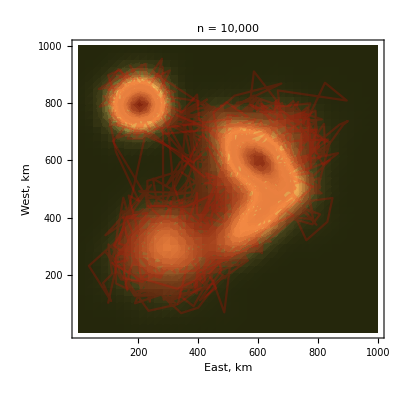

```mathematica
gb2=Show[SmoothDensityHistogram[lMediumList,Mesh->20,PlotLabel->"n = 10,000",PlotRange->{{0,10},{0,10}},Frame->{True,True,False,False},FrameLabel->{"East, km","North, km"},FrameTicks->{xTicks,xTicks},ColorFunction->"BrassTones"],ListLinePlot[lMediumList,PlotRange->{{0,10},{0,10}},PlotStyle->{Red,Opacity[0.2]}]]
```

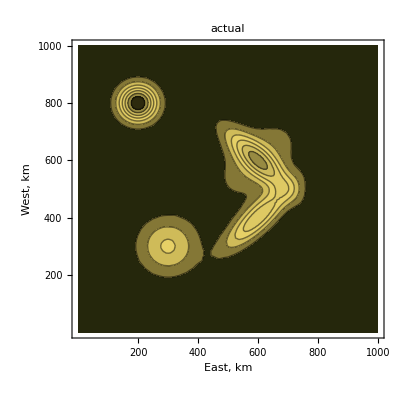

```mathematica
gbActual=ContourPlot[fRandomFunction[x,y],{x,0,10},{y,0,10},PlotRange->Full,Frame->{True,True,False,False},FrameLabel->{"East, km","North, km"},FrameTicks->{xTicks,xTicks},ColorFunction->"BrassTones",PlotLabel->"actual"]
```

```mathematica
gc1=SmoothHistogram3D[lShortList,Mesh->None,AxesLabel->{"East, km","North, km", ""},PlotRange->Full,ColorFunction->"BrassTones",Ticks->{xTicks,xTicks,None},ViewPoint->{1.4610778682878827,-1.9342706141474402,2.3608999669712687},ViewVertical->{0.,0.,1.},PlotLabel->"n = 1,000"]
```

-Graphics3D-

```mathematica
gc2=SmoothHistogram3D[lMediumList,Mesh->None,AxesLabel->{"East, km","North, km", ""},PlotRange->Full,ColorFunction->"BrassTones",Ticks->{xTicks,xTicks,None},ViewPoint->{1.4610778682878827,-1.9342706141474402,2.3608999669712687},ViewVertical->{0.,0.,1.},PlotLabel->"n = 10,000"]
```

-Graphics3D-

```mathematica
gc3=SmoothHistogram3D[lLongList,Mesh->None,AxesLabel->{"East, km","North, km", ""},PlotRange->Full,ColorFunction->"BrassTones",Ticks->{xTicks,xTicks,None},ViewPoint->{1.4610778682878827,-1.9342706141474402,2.3608999669712687},ViewVertical->{0.,0.,1.},PlotLabel->"n = 100,000"]
```

-Graphics3D-

```mathematica
gcActual=Plot3D[{fRandomFunction[x,y]},{x,0,10},{y,0,10},AxesLabel->{"East, km","North, km", ""},PlotRange->{Full,Full,{0,1}},ColorFunction->"BrassTones",Mesh->None,PlotPoints->20,Ticks->{xTicks,xTicks,None},ViewPoint->{1.4610778682878827,-1.9342706141474402,2.3608999669712687},ViewVertical->{0.,0.,1.},PlotLabel->"n = actual"]
```

-Graphics3D-

```mathematica
gFinal=Show[GraphicsGrid[{{gbActual,gb1,gb2,gb3},{gActual,g1,g2,g3},{gcActual,gc1,gc2,gc3}}],ImageSize->1500]
```

-Graphics-

```mathematica
Export["metropolisHastings_miningGoldMetropolis.png",gFinal]
```

metropolisHastings_miningGoldMetropolis.png